# Creator Style Space

## Rijksmuseum Semantic Explorer — Notebook 3 of 5

Every artwork in the Rijksmuseum collection is associated with one or more creators. By aggregating the embeddings of all works by a given artist into a single centroid vector, we construct a derived ‘style space’ where each point represents an artist rather than an individual artwork. This notebook explores that space: which artists are stylistically similar according to the embedding model? Do related artists cluster together in a hierarchical tree? Which artists have the most consistent output versus the widest stylistic range? The resulting creator map provides a novel, data-driven perspective on art-historical relationships within the Rijksmuseum collection.

## 1. Data Loading

```mathematica
dataDir = FileNameJoin[{NotebookDirectory[], "data"}];
If[!DirectoryQ[dataDir],
  Print["Data not found. Run: uv run python export_for_mathematica.py"];
  Abort[]];
manifest = Import[FileNameJoin[{dataDir, "metadata.json"}], "RawJSON"];
{n, dim} = Lookup[manifest, {"n", "dim"}];
raw = BinaryReadList[FileNameJoin[{dataDir, "embeddings.bin"}], "Real32"];
embeddings = Partition[raw, dim];
artIds = manifest["art_ids"];
artworks = manifest["artworks"];
Print["Loaded ", n, " embeddings"]
```

Loaded 20000 embeddings

## 2. Creator Frequency Analysis

The distribution of artworks per creator follows a power law, much like Zipf’s law in natural language: a handful of prolific artists and large studios account for a disproportionate share of the collection, while the vast majority of creators appear only once or a few times. This long-tail distribution has practical implications for our analysis — centroid embeddings are most meaningful for well-represented artists, since averaging over many works smooths out individual variation and yields a robust style signature. We set a minimum threshold of 10 works to ensure statistical reliability. The log-log frequency plot confirms the Zipfian shape.

Unique creators: 2761

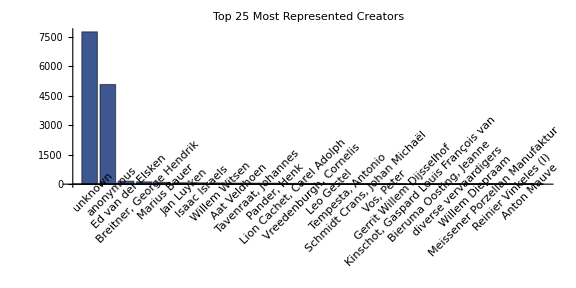

```mathematica
(* Primary creator for each artwork *)
creatorOf = Table[
  Module[{creators = artworks[ToString[id]]["creators"]},
    If[Length[creators] > 0, First[creators], "unknown"]],
  {id, artIds}];

creatorCounts = Counts[creatorOf];
Print["Unique creators: ", Length[creatorCounts]]

(* Top 25 most prolific *)
top25 = TakeLargest[creatorCounts, 25];
BarChart[Values[top25],
  ChartLabels -> Placed[Keys[top25], Below, Rotate[#, Pi/4, {-1, 0}] &],
  PlotLabel -> "Top 25 Most Represented Creators",
  ChartStyle -> "DarkRainbow",
  ImageSize -> Large,
  AspectRatio -> 1/2]
```

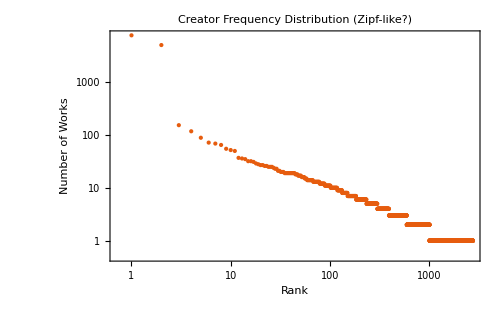

```mathematica
(* Creator frequency distribution (log-log) *)
freqDist = Reverse[Sort[Values[creatorCounts]]];
ListLogLogPlot[freqDist,
  PlotLabel -> "Creator Frequency Distribution (Zipf-like?)",
  AxesLabel -> {"Rank", "Number of Works"},
  PlotTheme -> "Scientific",
  PlotStyle -> PointSize[Small],
  ImageSize -> 500]
```

## 3. Creator Centroid Computation

The centroid embedding of a creator is the L2-normalised mean of all their artwork embeddings — a single vector summarising the artist’s average style as captured by the embedding model. For creators with many works, this centroid is a robust estimate of their stylistic centre of gravity; for those near the minimum threshold, it is noisier. We compute centroids for the top 100 most-represented creators, yielding a 100×384 matrix where each row is a creator’s style signature. This derived matrix forms the basis for all subsequent creator-level analyses: similarity matrices, dendrograms, and the 2D style map.

```mathematica
minWorks = 10;
qualified = Select[creatorCounts, # >= minWorks &];
topCreatorNames = Keys[TakeLargest[qualified, Min[100, Length[qualified]]]];
Print["Computing centroids for ", Length[topCreatorNames], " creators (>= ", minWorks, " works each)"]

creatorCentroids = Association[Table[
  Module[{mask, creatorEmbs},
    mask = Flatten[Position[creatorOf, name]];
    creatorEmbs = embeddings[[mask]];
    name -> Normalize[Mean[creatorEmbs]]],
  {name, topCreatorNames}]];

centroidMatrix = N[Values[creatorCentroids]]; (* nCreators x 384 *)
nCreators = Length[topCreatorNames];
Print["Centroid matrix: ", Dimensions[centroidMatrix]]
```

Computing centroids for 100 creators (>= 10 works each)

Centroid matrix: {100,384}

## 4. Creator Similarity Matrix

The creator similarity matrix shows all-pairs cosine similarity between centroid embeddings. A value near 1.0 means two artists produce semantically near-identical work in aggregate, while a value near 0 means their outputs occupy very different regions of embedding space. The full heatmap for 100 creators gives an overview: warm blocks along the diagonal indicate groups of similar creators, while isolated cool rows mark stylistically unique artists. The zoomed-in labelled view of the top 25 creators (by work count) makes it possible to identify specific artist-to-artist affinities — for instance, whether members of the same workshop or school cluster together.

```mathematica
creatorSimMat = centroidMatrix.Transpose[centroidMatrix];

(* Full matrix heatmap *)
MatrixPlot[creatorSimMat,
  PlotLabel -> "Creator Centroid Cosine Similarity (" <> ToString[nCreators] <> " creators)",
  ColorFunction -> "TemperatureMap",
  PlotLegends -> Automatic,
  ImageSize -> 600]
```

-Graphics-

```mathematica
(* Zoomed view of top 25 creators with labels *)
zoomN = Min[25, nCreators];
zoomNames = topCreatorNames[[1 ;; zoomN]];
zoomSim = creatorSimMat[[1 ;; zoomN, 1 ;; zoomN]];

MatrixPlot[zoomSim,
  FrameTicks -> {
    {Thread[{Range[zoomN], zoomNames}], None},
    {Thread[{Range[zoomN], zoomNames}], None}},
  PlotLabel -> "Top 25 Creator Similarity (labeled)",
  ColorFunction -> "TemperatureMap",
  PlotLegends -> Automatic,
  ImageSize -> 700]
```

-Graphics-

## 5. Hierarchical Style Clustering

Hierarchical clustering groups creators into a tree structure based on cosine distance between their centroid embeddings. The dendrogram visualises this hierarchy: artists joined at lower levels (shorter branches) are more similar, while those joined only at the top are most different. The branching pattern reveals stylistic families — clusters of artists whose work shares a common semantic signature. These groupings sometimes mirror art-historical relationships (same school, period, or medium), but can also surface less obvious connections that the embedding model detects from the visual and textual content of the artworks themselves.

```mathematica
(* Dendrogram of top creators by cosine distance *)
dendroN = Min[40, nCreators];
dendroNames = topCreatorNames[[1 ;; dendroN]];
dendroCentroids = centroidMatrix[[1 ;; dendroN]];

Dendrogram[
  MapThread[Rule, {dendroNames, dendroCentroids}],
  DistanceFunction -> CosineDistance,
  Bottom,
  DendrogramLayout -> "Horizontal",
  PlotLabel -> "Creator Style Dendrogram (cosine distance)",
  ImageSize -> {500, Max[400, dendroN * 18]}]
```

Dendrogram::nonopt: Options expected (instead of Bottom) beyond position 2 in Dendrogram[«1»]. An option must be a rule or a list of rules.

## 6. Intra-Artist Style Diversity

Not all artists produce homogeneous work. Some stick to a signature style (their works form a tight cluster near the centroid), while others experiment across genres, media, or subjects (their works scatter widely in embedding space). We quantify this using the mean cosine distance from each artist’s individual works to their centroid — a larger value means greater stylistic diversity. Plotting diversity against productivity (number of works) reveals whether prolific artists tend to diversify over a long career or instead specialise further. The tables of most diverse and most consistent creators make the abstract metric concrete with specific names.

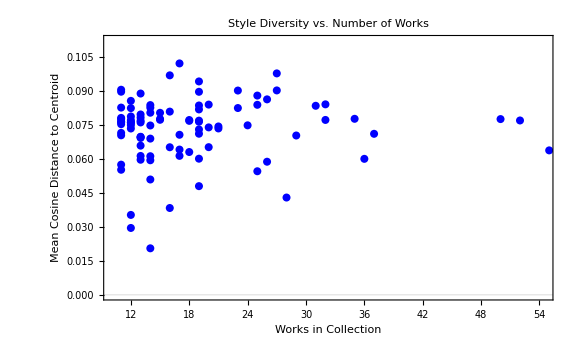

```mathematica
creatorDiversity = Association[Table[
  Module[{mask, creatorEmbs, centroid, dists},
    mask = Flatten[Position[creatorOf, name]];
    creatorEmbs = embeddings[[mask]];
    centroid = creatorCentroids[name];
    dists = 1 - creatorEmbs.centroid;
    name -> <|
      "meanDist" -> Mean[dists],
      "stdDist" -> If[Length[dists] > 1, StandardDeviation[dists], 0],
      "nWorks" -> Length[mask]|>],
  {name, topCreatorNames}]];

(* Diversity vs productivity *)
ListPlot[
  Table[
    Tooltip[
      {creatorDiversity[name]["nWorks"], creatorDiversity[name]["meanDist"]},
      name],
    {name, topCreatorNames}],
  PlotLabel -> "Style Diversity vs. Number of Works",
  AxesLabel -> {"Works in Collection", "Mean Cosine Distance to Centroid"},
  PlotStyle -> Directive[PointSize[0.01], Blue],
  PlotTheme -> "Scientific",
  ImageSize -> Large]
```

```mathematica
(* Most diverse vs most consistent creators *)
diversitySorted = Reverse[SortBy[Normal[creatorDiversity], #[[2]]["meanDist"] &]];

Print[Style["Most Diverse Creators (widest style range):", Bold]];
Grid[
  Prepend[
    Table[{diversitySorted[[i, 1]],
      NumberForm[diversitySorted[[i, 2]]["meanDist"], 3],
      diversitySorted[[i, 2]]["nWorks"]}, {i, 10}],
    Style[#, Bold] & /@ {"Creator", "Mean Distance", "Works"}],
  Frame -> All, Alignment -> {{Left, Center, Center}}]

Print[""];
Print[Style["Most Consistent Creators (tightest style):", Bold]];
Grid[
  Prepend[
    Table[{diversitySorted[[-i, 1]],
      NumberForm[diversitySorted[[-i, 2]]["meanDist"], 3],
      diversitySorted[[-i, 2]]["nWorks"]}, {i, 10}],
    Style[#, Bold] & /@ {"Creator", "Mean Distance", "Works"}],
  Frame -> All, Alignment -> {{Left, Center, Center}}]
```

Most Diverse Creators (widest style range):

Creator | Mean Distance | Works
anonymous | 0.112 | 5081
unknown | 0.107 | 7766
Charles Donker | 0.102 | 17
diverse vervaardigers | 0.0976 | 27
Fokke, Simon | 0.0967 | 16
Simon Frisius | 0.094 | 19
Jan Luyken | 0.0915 | 72
Heyboer, Anton | 0.0904 | 11
Bieruma Oosting, Jeanne | 0.0901 | 27
Brandes, Jan | 0.09 | 23

Most Consistent Creators (tightest style):

Creator | Mean Distance | Works
Immerzeel, Johannes | 0.0205 | 14
Cavalieri, Giovanni Battista de' | 0.0295 | 12
Mulder, Reinjan | 0.0352 | 12
Verenigde Oostindische Compagnie | 0.0383 | 16
Kinschot, Gaspard Louis François van | 0.0429 | 28
Doijer, Hendrik | 0.0479 | 19
Teding van Berkhout, jonkheer Hendrik (1879-1969) | 0.0508 | 14
Anton Mauve | 0.0545 | 25
Christoph Krieger | 0.0551 | 11
Sannes, Sanne | 0.0574 | 11

## 7. Most Similar Creator Pairs

Scanning all unique pairs of creators by centroid cosine similarity surfaces the most and least similar duos in the collection. High-similarity pairs may reflect direct artistic influence, shared workshop training, or simply working in the same genre and medium. Low-similarity pairs represent the greatest stylistic contrasts in the collection. These pairwise relationships complement the dendrogram: the tree shows hierarchical structure, while the ranked pairs highlight the extremes.

```mathematica
(* All unique pairs with similarity *)
pairs = Flatten[Table[
  {creatorSimMat[[i, j]], topCreatorNames[[i]], topCreatorNames[[j]]},
  {i, nCreators}, {j, i + 1, nCreators}], 1];
pairs = Reverse[SortBy[pairs, First]];

Print[Style["Top 20 Most Similar Creator Pairs:", Bold]];
Grid[
  Prepend[
    Table[{pairs[[i, 2]], pairs[[i, 3]], NumberForm[pairs[[i, 1]], 4]},
      {i, 20}],
    Style[#, Bold] & /@ {"Creator 1", "Creator 2", "Cosine Similarity"}],
  Frame -> All, Alignment -> {{Left, Left, Center}},
  Background -> {None, {LightBlue, {White, LightYellow}}}]
```

Top 20 Most Similar Creator Pairs:

Creator 1 | Creator 2 | Cosine Similarity
unknown | anonymous | 0.9941
unknown | Jan Luyken | 0.9848
Jan Luyken | Caspar Luyken | 0.9844
anonymous | Charles Donker | 0.9823
unknown | Bieruma Oosting, Jeanne | 0.9815
unknown | Charles Donker | 0.9806
anonymous | Jan Luyken | 0.9791
unknown | Velde, Jan van de (II) | 0.9791
unknown | Jessurun de Mesquita, Samuel | 0.9775
unknown | Lodewijk Schelfhout | 0.9773
anonymous | Bieruma Oosting, Jeanne | 0.9771
unknown | Graag, Julie de | 0.9769
anonymous | Jessurun de Mesquita, Samuel | 0.9767
unknown | Reinier Vinkeles (I) | 0.976
unknown | Storm van 's-Gravesande, Carel Nicolaas | 0.9756
unknown | Simon Frisius | 0.9755
unknown | Caspar Luyken | 0.9752
anonymous | Wijnberg, Nicolaas | 0.9752
anonymous | Willem Wenckebach | 0.975
anonymous | Velde, Jan van de (II) | 0.975

```mathematica
Print[Style["\nMost Dissimilar Creator Pairs:", Bold]];
Grid[
  Prepend[
    Table[{pairs[[-i, 2]], pairs[[-i, 3]], NumberForm[pairs[[-i, 1]], 4]},
      {i, 10}],
    Style[#, Bold] & /@ {"Creator 1", "Creator 2", "Cosine Similarity"}],
  Frame -> All, Alignment -> {{Left, Left, Center}}]
```

Most Dissimilar Creator Pairs:

Creator 1 | Creator 2 | Cosine Similarity
Doijer, Hendrik | Cavalieri, Giovanni Battista de' | 0.8321
Verenigde Oostindische Compagnie | Immerzeel, Johannes | 0.8347
Doijer, Hendrik | Verenigde Oostindische Compagnie | 0.8442
Immerzeel, Johannes | Sannes, Sanne | 0.8451
Kinschot, Gaspard Louis François van | Doijer, Hendrik | 0.8452
Cavalieri, Giovanni Battista de' | Mulder, Reinjan | 0.8453
Verenigde Oostindische Compagnie | Sannes, Sanne | 0.8506
Verenigde Oostindische Compagnie | Teding van Berkhout, jonkheer Hendrik (1879-1969) | 0.8509
Anton Mauve | Verenigde Oostindische Compagnie | 0.851
Cavalieri, Giovanni Battista de' | Sannes, Sanne | 0.8516

## 8. 2D Creator Style Map

Applying PCA to the 100×384 centroid matrix and projecting onto the first two components gives a two-dimensional map where proximity reflects stylistic similarity. Point size encodes the number of works in the collection (larger dots for more prolific artists), while colour encodes style diversity (blue for consistent artists, red for diverse ones). Prolific artists with consistent styles appear as large blue dots, while wide-ranging experimenters are large red dots. The spatial arrangement reveals whether the creator landscape has clear regions or whether styles blend continuously.

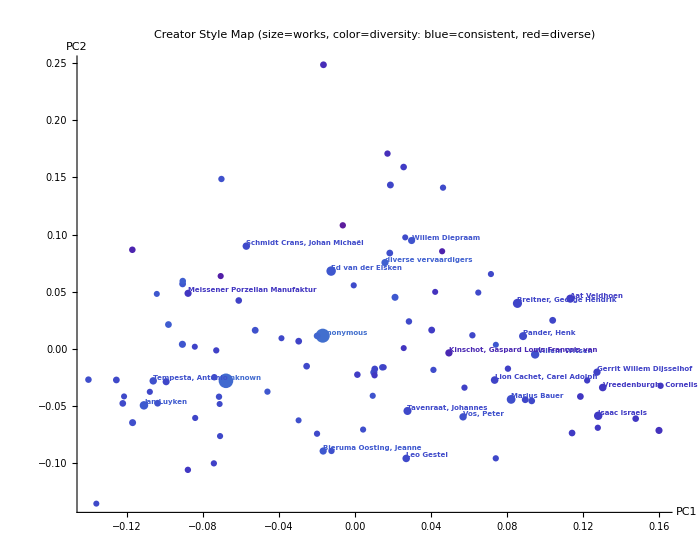

```mathematica
(* PCA of creator centroids *)
centroidMu = Mean[centroidMatrix];
centroidCentered = centroidMatrix - ConstantArray[centroidMu, nCreators];
centroidCov = Transpose[centroidCentered].centroidCentered;
{cVals, cVecs} = Eigensystem[centroidCov];
cOrder = Reverse[Ordering[cVals]];

(* Project onto first 2 PCs *)
creatorPC = centroidCentered.Transpose[{cVecs[[cOrder[[1]]]], cVecs[[cOrder[[2]]]]}];

(* Size proportional to log(number of works) *)
Graphics[
  Table[
    Module[{pt = creatorPC[[i]], name = topCreatorNames[[i]],
            nw = creatorDiversity[topCreatorNames[[i]]]["nWorks"]},
      {ColorData["Rainbow"][creatorDiversity[name]["meanDist"] / 0.5],
       PointSize[0.003 + 0.012 Log[nw] / Log[Max[Values[creatorCounts]]]],
       Point[pt],
       If[nw > Quantile[Values[qualified], 0.8],
         Text[Style[name, 7, Bold], pt, {-1.1, -0.5}],
         Nothing]}
    ],
    {i, nCreators}],
  Axes -> True,
  AxesLabel -> {"PC1", "PC2"},
  PlotLabel -> "Creator Style Map\n(size=works, color=diversity: blue=consistent, red=diverse)",
  ImageSize -> 700,
  AspectRatio -> 0.8]
```